#### Example 2: Empirically determine the variance of a two-mode squeezed vacuum state and compare with theory

```mathematica
(*Loading the MENTAT package *)
<<"C:\\Users\\uqnzaund\\OneDrive - The University of Queensland\\Desktop\\Index\\Side projects\\Mentat\\MENTAT\\MENTAT.wl"
```

@MENTAT: Clearing kernel...

@MENTAT: Loading package...

@MENTAT: All functions loaded. 
Welcome to MENTAT, a computer algebra system for Fock-state calculations in bosonic optical systems! Copyright N. Zaunders, University of Queensland, 2024. All rights reserved.

```mathematica
(* Define a two-mode squeezed vacuum state with squeezing parameter χ. The TMSVS is a continuous state and so is infinite-dimensional, so we choose to truncate to n = 6 / dimension 6. *)
ψAB=TwoModeSqueezedVacuumState[χ,n->6]
```

√(1-χ^2) 0,0+χ √(1-χ^2) 1,1+χ^2 √(1-χ^2) 2,2+χ^3 √(1-χ^2) 3,3+χ^4 √(1-χ^2) 4,4+χ^5 √(1-χ^2) 5,5+χ^6 √(1-χ^2) 6,6

```mathematica
(* Define the position quadrature operators Subscript[q̂, A,B] in the usual fashion. The subscript indicates what mode the operators correspond to. *)
qA=SuperDagger[Subscript[â, 1]]+Subscript[â, 1]
qB=SuperDagger[Subscript[b̂, 2]]+Subscript[b̂, 2]
```

(â)_1+((â)_1)^†

(b̂)_2+((b̂)_2)^†

```mathematica
(* Evaluate the quadrature mean Subscript[μ, A,B] = ⟨Subscript[q̂, A,B]⟩ by taking the expectation value of the operator w.r.t to the pure state ψAB. 
As expected for the vacuum state, the mean values are zero. *)
meanA=SuperDagger[ψAB]·qA·ψAB
meanB=SuperDagger[ψAB]·qB·ψAB
```

0

0

```mathematica
(* Determine the quadrature covariances Subscript[Var, Subscript[q̂, i],Subscript[q̂, j]] = ⟨Subscript[q̂, i] Subscript[q̂, j]⟩-⟨Subscript[q̂, i]⟩⟨Subscript[q̂, j]⟩ w.r.t to the pure state ψAB. *)
covarAA=SuperDagger[ψAB]·(qA·qA)·ψAB-(SuperDagger[ψAB]·qA·ψAB)^2
covarBB=SuperDagger[ψAB]·(qB·qB)·ψAB-(SuperDagger[ψAB]·qB·ψAB)^2
covarAB=SuperDagger[ψAB]·(qA·qB)·ψAB-(SuperDagger[ψAB]·qA·ψAB)*(SuperDagger[ψAB]·qB·ψAB)
covarBA=SuperDagger[ψAB]·(qB·qA)·ψAB-(SuperDagger[ψAB]·qB·ψAB)*(SuperDagger[ψAB]·qA·ψAB)
```

√(1-χ^2) Conjugate[√(1-χ^2)]+5 χ^2 √(1-χ^2) Conjugate[χ]^2 Conjugate[√(1-χ^2)]+7 χ^3 √(1-χ^2) Conjugate[χ]^3 Conjugate[√(1-χ^2)]+9 χ^4 √(1-χ^2) Conjugate[χ]^4 Conjugate[√(1-χ^2)]+11 χ^5 √(1-χ^2) Conjugate[χ]^5 Conjugate[√(1-χ^2)]+13 χ^6 √(1-χ^2) Conjugate[χ]^6 Conjugate[√(1-χ^2)]+3 χ √(1-χ^2) Conjugate[χ √(1-χ^2)]

√(1-χ^2) Conjugate[√(1-χ^2)]+5 χ^2 √(1-χ^2) Conjugate[χ]^2 Conjugate[√(1-χ^2)]+7 χ^3 √(1-χ^2) Conjugate[χ]^3 Conjugate[√(1-χ^2)]+9 χ^4 √(1-χ^2) Conjugate[χ]^4 Conjugate[√(1-χ^2)]+11 χ^5 √(1-χ^2) Conjugate[χ]^5 Conjugate[√(1-χ^2)]+13 χ^6 √(1-χ^2) Conjugate[χ]^6 Conjugate[√(1-χ^2)]+3 χ √(1-χ^2) Conjugate[χ √(1-χ^2)]

χ √(1-χ^2) Conjugate[√(1-χ^2)]+2 χ √(1-χ^2) Conjugate[χ]^2 Conjugate[√(1-χ^2)]+3 χ^3 √(1-χ^2) Conjugate[χ]^2 Conjugate[√(1-χ^2)]+3 χ^2 √(1-χ^2) Conjugate[χ]^3 Conjugate[√(1-χ^2)]+4 χ^4 √(1-χ^2) Conjugate[χ]^3 Conjugate[√(1-χ^2)]+4 χ^3 √(1-χ^2) Conjugate[χ]^4 Conjugate[√(1-χ^2)]+5 χ^5 √(1-χ^2) Conjugate[χ]^4 Conjugate[√(1-χ^2)]+5 χ^4 √(1-χ^2) Conjugate[χ]^5 Conjugate[√(1-χ^2)]+6 χ^6 √(1-χ^2) Conjugate[χ]^5 Conjugate[√(1-χ^2)]+6 χ^5 √(1-χ^2) Conjugate[χ]^6 Conjugate[√(1-χ^2)]+√(1-χ^2) Conjugate[χ √(1-χ^2)]+2 χ^2 √(1-χ^2) Conjugate[χ √(1-χ^2)]

χ √(1-χ^2) Conjugate[√(1-χ^2)]+2 χ √(1-χ^2) Conjugate[χ]^2 Conjugate[√(1-χ^2)]+3 χ^3 √(1-χ^2) Conjugate[χ]^2 Conjugate[√(1-χ^2)]+3 χ^2 √(1-χ^2) Conjugate[χ]^3 Conjugate[√(1-χ^2)]+4 χ^4 √(1-χ^2) Conjugate[χ]^3 Conjugate[√(1-χ^2)]+4 χ^3 √(1-χ^2) Conjugate[χ]^4 Conjugate[√(1-χ^2)]+5 χ^5 √(1-χ^2) Conjugate[χ]^4 Conjugate[√(1-χ^2)]+5 χ^4 √(1-χ^2) Conjugate[χ]^5 Conjugate[√(1-χ^2)]+6 χ^6 √(1-χ^2) Conjugate[χ]^5 Conjugate[√(1-χ^2)]+6 χ^5 √(1-χ^2) Conjugate[χ]^6 Conjugate[√(1-χ^2)]+√(1-χ^2) Conjugate[χ √(1-χ^2)]+2 χ^2 √(1-χ^2) Conjugate[χ √(1-χ^2)]

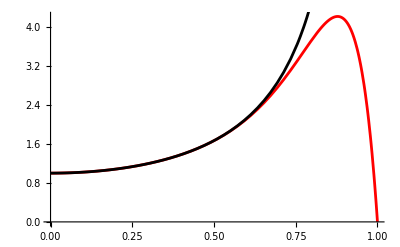

```mathematica
(* Show that our calculated covariance of the 'A' mode (red) approximates the true analytic solution (black).
This example also shows that our derived covariance loses accuracy for large values of χ, where the truncation of the state causes a significant deviation from the true state. *)
Show[
Plot[covarAA,{χ,0,1},PlotRange->Full,PlotStyle->Red],
Plot[(1+χ^2)/(1-χ^2),{χ,0,1},PlotRange->Full,PlotStyle->Black]
]
```